```mathematica
1/(1+exp(-z))
```

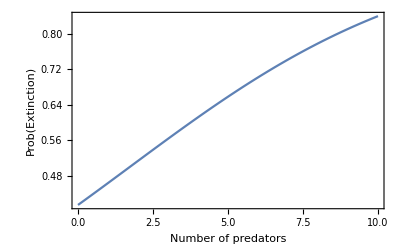

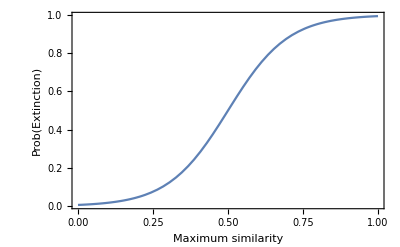

```mathematica
Plot[1/(1+Exp[-0.2(x-(L/S))])/.{L->165,S->96},{x,0,10},PlotRange->All,Frame->True,FrameLabel->{"Number of predators","Prob(Extinction)"}]
Plot[1/(1+Exp[-10*(y-0.5)]),{y,0,1},PlotRange->All,Frame->True,FrameLabel->{"Maximum similarity","Prob(Extinction)"}]
```

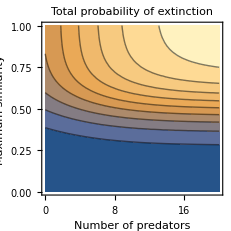

```mathematica
ContourPlot[1/(1+Exp[-0.2(x-(L/S))])*1/(1+Exp[-10*(y-0.5)])/.{L->165,S->96},{x,0,20},{y,0,1},PlotRange->All,FrameLabel->{"Number of predators","Maximum similarity"},PlotLabel->"Total probability of extinction"]
```